```mathematica
HH=Table[A[i][j],{i,4},{j,4}]
```

{{A[1][1],A[1][2],A[1][3],A[1][4]},{A[2][1],A[2][2],A[2][3],A[2][4]},{A[3][1],A[3][2],A[3][3],A[3][4]},{A[4][1],A[4][2],A[4][3],A[4][4]}}

```mathematica
For[i=1,i≤4,i++,For[j=1,j≤4,j++,A[i][j]=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]]];
```

```mathematica
MatrixForm[HH]
```

((0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)
(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)
(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)
(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1))

```mathematica
Flatten[%6]
```

### Define Σij=σi@σj

```mathematica
For[i=0,i≤3,i++,For[j=0,j≤3,j++,Σ[i][j]=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]]];
```

### Define Hamiltonian with parameters

```mathematica
M=2.5;
t0=1;
t0'=1;
t0''=1;
t=1;
t'=1;
t''=1;
```

```mathematica
Ham[kx_,ky_,kz_,ϕ_]:=(M-t0 Cos[kx-ϕ]-t0' Cos[ky]-t0'' Cos[kz])Σ[0][3]+t Sin[(kx-ϕ)/2](Sin[kx/2] Σ[1][1]+Cos[kx/2] Σ[2][1])+t' Sin[ky] Σ[0][2]+t'' Sin[kz]Σ[3][1]
```

```mathematica
MatrixForm[Ham[kx,ky,kz,ϕ]]
```

### Define perturbation for double Copies Hamiltonian

```mathematica
P11=0.82;
P12=0.91;
P111=0.12;
P112=0.13;
P113=0.05;
P121=0.11;
P122=0.14;
P123=0.24;
Per=P123 KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],PauliMatrix[1]]];
```

```mathematica
MatrixForm[Per]
```

(0. | 0. | 0. | 0. | 0. | 0.24 | 0. | 0.
0. | 0. | 0. | 0. | 0.24 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.24
0. | 0. | 0. | 0. | 0. | 0. | 0.24 | 0.
0. | 0.24 | 0. | 0. | 0. | 0. | 0. | 0.
0.24 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.24 | 0. | 0. | 0. | 0.
0. | 0. | 0.24 | 0. | 0. | 0. | 0. | 0.)

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
MatrixForm[Per]
```

(0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.041-0.2184 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.029-0.2067 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.041+0.2184 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.2258-0.0065 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.041-0.2184 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.029-0.2067 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.041+0.2184 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.2258-0.0065 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.2258+0.0065 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.041+0.2184 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.029+0.2067 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.041-0.2184 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.2258+0.0065 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.041+0.2184 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.029+0.2067 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.041-0.2184 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

### Enlarge the Hamiltonian with Identity copy, with different tune parameters

```mathematica
DHam[kx_,ky_,kz_,ϕ1_,ϕ2_]:=Per+({{2.5-Cos[kx-ϕ1]-Cos[ky]-Cos[kz], -ⅈ Sin[ky]+Sin[kz], 0, (-ⅈ Cos[(kx-ϕ1)/2]+Sin[(kx-ϕ1)/2]) Sin[(kx-ϕ1)/2], 0, 0, 0, 0}, {ⅈ Sin[ky]+Sin[kz], -2.5+Cos[kx-ϕ1]+Cos[ky]+Cos[kz], (-ⅈ Cos[(kx-ϕ1)/2]+Sin[(kx-ϕ1)/2]) Sin[(kx-ϕ1)/2], 0, 0, 0, 0, 0}, {0, (ⅈ Cos[(kx-ϕ1)/2]+Sin[(kx-ϕ1)/2]) Sin[(kx-ϕ1)/2], 2.5-Cos[kx-ϕ1]-Cos[ky]-Cos[kz], -ⅈ Sin[ky]-Sin[kz], 0, 0, 0, 0}, {(ⅈ Cos[(kx-ϕ1)/2]+Sin[(kx-ϕ1)/2]) Sin[(kx-ϕ1)/2], 0, ⅈ Sin[ky]-Sin[kz], -2.5+Cos[kx-ϕ1]+Cos[ky]+Cos[kz], 0, 0, 0, 0}, {0, 0, 0, 0, 2.5-Cos[kx-ϕ2]-Cos[ky]-Cos[kz], -ⅈ Sin[ky]+Sin[kz], 0, (-ⅈ Cos[(kx-ϕ2)/2]+Sin[(kx-ϕ2)/2]) Sin[(kx-ϕ2)/2]}, {0, 0, 0, 0, ⅈ Sin[ky]+Sin[kz], -2.5+Cos[kx-ϕ2]+Cos[ky]+Cos[kz], (-ⅈ Cos[(kx-ϕ2)/2]+Sin[(kx-ϕ2)/2]) Sin[(kx-ϕ2)/2], 0}, {0, 0, 0, 0, 0, (ⅈ Cos[(kx-ϕ2)/2]+Sin[(kx-ϕ2)/2]) Sin[(kx-ϕ2)/2], 2.5-Cos[kx-ϕ2]-Cos[ky]-Cos[kz], -ⅈ Sin[ky]-Sin[kz]}, {0, 0, 0, 0, (ⅈ Cos[(kx-ϕ2)/2]+Sin[(kx-ϕ2)/2]) Sin[(kx-ϕ2)/2], 0, ⅈ Sin[ky]-Sin[kz], -2.5+Cos[kx-ϕ2]+Cos[ky]+Cos[kz]}});
```

```mathematica
MatrixForm[DHam[kx,ky,kz,ϕ1,ϕ2]]
```

(2.5-Cos[ky]-Cos[kz]-Cos[kx-ϕ1] | 0.-ⅈ Sin[ky]+Sin[kz] | 0. | 0.+Sin[(kx-ϕ1)/2] (-ⅈ Cos[(kx-ϕ1)/2]+Sin[(kx-ϕ1)/2]) | 0. | 0.24 | 0. | 0.
0.+ⅈ Sin[ky]+Sin[kz] | -2.5+Cos[ky]+Cos[kz]+Cos[kx-ϕ1] | 0.+Sin[(kx-ϕ1)/2] (-ⅈ Cos[(kx-ϕ1)/2]+Sin[(kx-ϕ1)/2]) | 0. | 0.24 | 0. | 0. | 0.
0. | 0.+Sin[(kx-ϕ1)/2] (ⅈ Cos[(kx-ϕ1)/2]+Sin[(kx-ϕ1)/2]) | 2.5-Cos[ky]-Cos[kz]-Cos[kx-ϕ1] | 0.-ⅈ Sin[ky]-Sin[kz] | 0. | 0. | 0. | 0.24
0.+Sin[(kx-ϕ1)/2] (ⅈ Cos[(kx-ϕ1)/2]+Sin[(kx-ϕ1)/2]) | 0. | 0.+ⅈ Sin[ky]-Sin[kz] | -2.5+Cos[ky]+Cos[kz]+Cos[kx-ϕ1] | 0. | 0. | 0.24 | 0.
0. | 0.24 | 0. | 0. | 2.5-Cos[ky]-Cos[kz]-Cos[kx-ϕ2] | 0.-ⅈ Sin[ky]+Sin[kz] | 0. | 0.+Sin[(kx-ϕ2)/2] (-ⅈ Cos[(kx-ϕ2)/2]+Sin[(kx-ϕ2)/2])
0.24 | 0. | 0. | 0. | 0.+ⅈ Sin[ky]+Sin[kz] | -2.5+Cos[ky]+Cos[kz]+Cos[kx-ϕ2] | 0.+Sin[(kx-ϕ2)/2] (-ⅈ Cos[(kx-ϕ2)/2]+Sin[(kx-ϕ2)/2]) | 0.
0. | 0. | 0. | 0.24 | 0. | 0.+Sin[(kx-ϕ2)/2] (ⅈ Cos[(kx-ϕ2)/2]+Sin[(kx-ϕ2)/2]) | 2.5-Cos[ky]-Cos[kz]-Cos[kx-ϕ2] | 0.-ⅈ Sin[ky]-Sin[kz]
0. | 0. | 0.24 | 0. | 0.+Sin[(kx-ϕ2)/2] (ⅈ Cos[(kx-ϕ2)/2]+Sin[(kx-ϕ2)/2]) | 0. | 0.+ⅈ Sin[ky]-Sin[kz] | -2.5+Cos[ky]+Cos[kz]+Cos[kx-ϕ2])

### Define dispersion function and plot of original function

```mathematica
F[kx_,ky_,kz_,ϕ_]:=Sort[N[Eigenvalues[Ham[kx+0.0,ky+0.0,kz+0.0,ϕ]]]];
```

```mathematica
Plot3D[F[kx,ky,0,0.4],{kx,-Pi,Pi},{ky,-Pi,Pi}]
```

-Graphics3D-

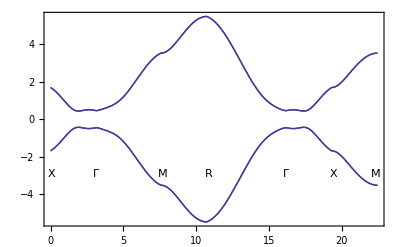

```mathematica
Plot[Piecewise[{{F[Pi-tt,0,0,0.5],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0,0.5],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi,0.5],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],0.5],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0,0.5],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0,0.5],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi},GridLines->{{{Pi,Dashed},{(1+Sqrt[2])Pi,Dashed},{(Sqrt[2]+2)Pi,Dashed},{(2+Sqrt[2]+Sqrt[3])Pi,Dashed},{(3+Sqrt[2]+Sqrt[3])Pi,Dashed},{(4+Sqrt[2]+Sqrt[3])Pi,Dashed}},{}},Epilog->{Inset["X",{0.05,0.08-3}],Inset["Γ",{Pi,0.08-3}],Inset["M",{(1+Sqrt[2])Pi+0.15,0.08-3}],Inset["R",{(2+Sqrt[2])Pi+0.15,0.08-3}],Inset["Γ",{(2+Sqrt[2]+Sqrt[3])Pi,0.08-3}],Inset["X",{(3+Sqrt[2]+Sqrt[3])Pi+0.15,0.08-3}],Inset["M",{(4+Sqrt[2]+Sqrt[3])Pi-0.15,0.08-3}]},Frame->True]
```

### Define dispersion relation and plot of Double Hamiltonian

```mathematica
DF[kx_,ky_,kz_]:=Sort[N[Eigenvalues[DHam[kx+0.0,ky+0.0,kz+0.0,-Pi+0.01,Pi+0.03]]]];
```

```mathematica
DF[0,0,0]
```

{-1.94594,-1.94594,-1.6813,-1.6813,1.6813,1.6813,1.94594,1.94594}

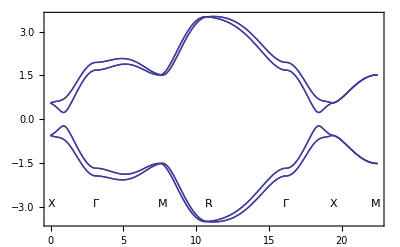

```mathematica
Plot[Piecewise[{{DF[Pi-tt,0,0],tt≥0&&tt<Pi},{DF[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{DF[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{DF[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{DF[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{DF[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi},GridLines->{{{Pi,Dashed},{(1+Sqrt[2])Pi,Dashed},{(Sqrt[2]+2)Pi,Dashed},{(2+Sqrt[2]+Sqrt[3])Pi,Dashed},{(3+Sqrt[2]+Sqrt[3])Pi,Dashed},{(4+Sqrt[2]+Sqrt[3])Pi,Dashed}},{}},Epilog->{Inset["X",{0.05,0.08-3}],Inset["Γ",{Pi,0.08-3}],Inset["M",{(1+Sqrt[2])Pi+0.15,0.08-3}],Inset["R",{(2+Sqrt[2])Pi+0.15,0.08-3}],Inset["Γ",{(2+Sqrt[2]+Sqrt[3])Pi,0.08-3}],Inset["X",{(3+Sqrt[2]+Sqrt[3])Pi+0.15,0.08-3}],Inset["M",{(4+Sqrt[2]+Sqrt[3])Pi-0.15,0.08-3}]},Frame->True]
```

### Find the eigensystem and choose the two lower bands as VEC

```mathematica
ESYS[kx_,ky_,kz_]:=Eigensystem[Ham[kx,ky,kz,Pi/2]]
```

```mathematica
VEC[kx_,ky_,kz_]:=(Clear[VEC1,VEC2];For[i=1;j=1,i≤4,i++,If[ESYS[kx,ky,kz][[1]][[i]]<0,If[j==1,VEC1=ESYS[kx,ky,kz][[2]][[i]];j++,VEC2=ESYS[kx,ky,kz][[2]][[i]]]]];{VEC1,VEC2})
```

```mathematica
VEC[1,1,1]
```

{{0.434593+0.286895 ⅈ,-0.169423-0.827609 ⅈ,0.122772+0.0102721 ⅈ,0.},{-0.0346859-0.118217 ⅈ,0.,0.368225+0.368225 ⅈ,0.844773}}

```mathematica
VEC[1,1,1][[1]]
```

{0.434593+0.286895 ⅈ,-0.169423-0.827609 ⅈ,0.122772+0.0102721 ⅈ,0.}

### Build correlation function C[x,x’]

#### define numerical integral function

```mathematica
INT[y_,kx_,kz_,LL_,HL_,i_,j_]:=(Clear[int];
For[ii=LL;int=0,ii≤HL,ii=ii+0.05,int+=0.05y[kx,ii,kz,i,j]];int)
```

#### define the Core of Correlation function for integral

```mathematica
CORE[kx_,ky_,kz_,i_,j_]:=Exp[I (i-j) ky](KroneckerProduct[Conjugate[VEC[kx,ky,kz][[1]]],VEC[kx,ky,kz][[1]]]+KroneckerProduct[Conjugate[VEC[kx,ky,kz][[2]]],VEC[kx,ky,kz][[2]]])
```

#### define the Correlation function matrix, with 24 by 24

```mathematica
HCOR[kx_,kz_]:=(Clear[COR];Clear[OUT];OUT=Table[COR[i][j],{i,6},{j,6}];For[iii=1,iii≤6,iii++,For[jjj=1,jjj≤6,jjj++,COR[iii][jjj]=INT[CORE ,kx,kz,-Pi,Pi,iii,jjj]]];OUT=ArrayFlatten[OUT])
```

```mathematica
MatrixForm[N[HCOR[1,1]]]
```

(1.28932+0. ⅈ | -1.74944-0.0000607439 ⅈ | -2.41235×10^-17+3.52149×10^-17 ⅈ | -0.164793+0.561652 ⅈ | 0.591636-0.0000108288 ⅈ | -1.35053+0.000111867 ⅈ | 3.30187×10^-18-1.08225×10^-18 ⅈ | -0.0367742+0.125395 ⅈ | 0.0893046+0.0000216606 ⅈ | -0.339218-0.000163021 ⅈ | 5.42505×10^-18+5.65801×10^-19 ⅈ | -0.0126442+0.0429726 ⅈ | 0.0241835-0.0000324984 ⅈ | -0.111717+0.00021422 ⅈ | -7.22586×10^-18+1.51497×10^-17 ⅈ | -0.00418963+0.0144615 ⅈ | 0.00896345+0.0000433453 ⅈ | -0.0458109-0.00026548 ⅈ | -1.07356×10^-17+1.72048×10^-17 ⅈ | -0.00210047+0.00691571 ⅈ | 0.00236498-0.0000542043 ⅈ | -0.0135081+0.000316813 ⅈ | 1.22788×10^-18+1.08507×10^-17 ⅈ | -0.000318793+0.00139058 ⅈ
-1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.164793+0.561652 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.569394-9.63815×10^-6 ⅈ | -0.60845-0.000268185 ⅈ | -0.0367742+0.125395 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.0714542-0.0000414649 ⅈ | -0.072493+0.000536444 ⅈ | -0.0126442+0.0429726 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.0217169+0.0000925796 ⅈ | -0.0409914-0.000804853 ⅈ | -0.00418963+0.0144615 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.00260854-0.00014372 ⅈ | 0.00783905+0.00107349 ⅈ | -0.00210047+0.00691571 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.00499545+0.000194901 ⅈ | -0.0191606-0.00134242 ⅈ | -0.000318793+0.00139058 ⅈ | 0.+3.46945×10^-19 ⅈ
-2.41235×10^-17-3.52149×10^-17 ⅈ | -0.164793-0.561652 ⅈ | 1.28932+0. ⅈ | 1.74944-0.0000607439 ⅈ | -4.21965×10^-19+3.35844×10^-17 ⅈ | -0.036807-0.125386 ⅈ | 0.591636-0.0000108288 ⅈ | -0.569394+9.63815×10^-6 ⅈ | 4.99792×10^-19-3.37811×10^-17 ⅈ | -0.0125785-0.0429919 ⅈ | 0.0893046+0.0000216606 ⅈ | -0.0714542+0.0000414649 ⅈ | 1.06819×10^-17-9.00821×10^-18 ⅈ | -0.00428813-0.0144326 ⅈ | 0.0241835-0.0000324984 ⅈ | -0.0217169-0.0000925796 ⅈ | 5.88242×10^-18+3.50673×10^-18 ⅈ | -0.00196909-0.00695426 ⅈ | 0.00896345+0.0000433453 ⅈ | -0.00260854+0.00014372 ⅈ | 1.13502×10^-17+2.52963×10^-17 ⅈ | -0.000483077-0.00134237 ⅈ | 0.00236498-0.0000542043 ⅈ | -0.00499545-0.000194901 ⅈ
-0.164793-0.561652 ⅈ | 0.+3.46945×10^-19 ⅈ | 1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.036807-0.125386 ⅈ | 0.-3.46945×10^-19 ⅈ | 1.35053-0.000111867 ⅈ | -0.60845-0.000268185 ⅈ | -0.0125785-0.0429919 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.339218+0.000163021 ⅈ | -0.072493+0.000536444 ⅈ | -0.00428813-0.0144326 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.111717-0.00021422 ⅈ | -0.0409914-0.000804853 ⅈ | -0.00196909-0.00695426 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.0458109+0.00026548 ⅈ | 0.00783905+0.00107349 ⅈ | -0.000483077-0.00134237 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.0135081-0.000316813 ⅈ | -0.0191606-0.00134242 ⅈ
0.591636+0.0000108288 ⅈ | 0.569394+9.63815×10^-6 ⅈ | -4.21965×10^-19-3.35844×10^-17 ⅈ | -0.036807+0.125386 ⅈ | 1.28932+0. ⅈ | -1.74944-0.0000607439 ⅈ | -2.41235×10^-17+3.52149×10^-17 ⅈ | -0.164793+0.561652 ⅈ | 0.591636-0.0000108288 ⅈ | -1.35053+0.000111867 ⅈ | 3.30187×10^-18-1.08225×10^-18 ⅈ | -0.0367742+0.125395 ⅈ | 0.0893046+0.0000216606 ⅈ | -0.339218-0.000163021 ⅈ | 5.42505×10^-18+5.65801×10^-19 ⅈ | -0.0126442+0.0429726 ⅈ | 0.0241835-0.0000324984 ⅈ | -0.111717+0.00021422 ⅈ | -7.22586×10^-18+1.51497×10^-17 ⅈ | -0.00418963+0.0144615 ⅈ | 0.00896345+0.0000433453 ⅈ | -0.0458109-0.00026548 ⅈ | -1.07356×10^-17+1.72048×10^-17 ⅈ | -0.00210047+0.00691571 ⅈ
-1.35053-0.000111867 ⅈ | -0.60845+0.000268185 ⅈ | -0.036807+0.125386 ⅈ | 0.+3.46945×10^-19 ⅈ | -1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.164793+0.561652 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.569394-9.63815×10^-6 ⅈ | -0.60845-0.000268185 ⅈ | -0.0367742+0.125395 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.0714542-0.0000414649 ⅈ | -0.072493+0.000536444 ⅈ | -0.0126442+0.0429726 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.0217169+0.0000925796 ⅈ | -0.0409914-0.000804853 ⅈ | -0.00418963+0.0144615 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.00260854-0.00014372 ⅈ | 0.00783905+0.00107349 ⅈ | -0.00210047+0.00691571 ⅈ | 0.-3.46945×10^-19 ⅈ
3.30187×10^-18+1.08225×10^-18 ⅈ | -0.0367742-0.125395 ⅈ | 0.591636+0.0000108288 ⅈ | 1.35053+0.000111867 ⅈ | -2.41235×10^-17-3.52149×10^-17 ⅈ | -0.164793-0.561652 ⅈ | 1.28932+0. ⅈ | 1.74944-0.0000607439 ⅈ | -4.21965×10^-19+3.35844×10^-17 ⅈ | -0.036807-0.125386 ⅈ | 0.591636-0.0000108288 ⅈ | -0.569394+9.63815×10^-6 ⅈ | 4.99792×10^-19-3.37811×10^-17 ⅈ | -0.0125785-0.0429919 ⅈ | 0.0893046+0.0000216606 ⅈ | -0.0714542+0.0000414649 ⅈ | 1.06819×10^-17-9.00821×10^-18 ⅈ | -0.00428813-0.0144326 ⅈ | 0.0241835-0.0000324984 ⅈ | -0.0217169-0.0000925796 ⅈ | 5.88242×10^-18+3.50673×10^-18 ⅈ | -0.00196909-0.00695426 ⅈ | 0.00896345+0.0000433453 ⅈ | -0.00260854+0.00014372 ⅈ
-0.0367742-0.125395 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.569394-9.63815×10^-6 ⅈ | -0.60845+0.000268185 ⅈ | -0.164793-0.561652 ⅈ | 0.+3.46945×10^-19 ⅈ | 1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.036807-0.125386 ⅈ | 0.-3.46945×10^-19 ⅈ | 1.35053-0.000111867 ⅈ | -0.60845-0.000268185 ⅈ | -0.0125785-0.0429919 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.339218+0.000163021 ⅈ | -0.072493+0.000536444 ⅈ | -0.00428813-0.0144326 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.111717-0.00021422 ⅈ | -0.0409914-0.000804853 ⅈ | -0.00196909-0.00695426 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.0458109+0.00026548 ⅈ | 0.00783905+0.00107349 ⅈ
0.0893046-0.0000216606 ⅈ | 0.0714542+0.0000414649 ⅈ | 4.99792×10^-19+3.37811×10^-17 ⅈ | -0.0125785+0.0429919 ⅈ | 0.591636+0.0000108288 ⅈ | 0.569394+9.63815×10^-6 ⅈ | -4.21965×10^-19-3.35844×10^-17 ⅈ | -0.036807+0.125386 ⅈ | 1.28932+0. ⅈ | -1.74944-0.0000607439 ⅈ | -2.41235×10^-17+3.52149×10^-17 ⅈ | -0.164793+0.561652 ⅈ | 0.591636-0.0000108288 ⅈ | -1.35053+0.000111867 ⅈ | 3.30187×10^-18-1.08225×10^-18 ⅈ | -0.0367742+0.125395 ⅈ | 0.0893046+0.0000216606 ⅈ | -0.339218-0.000163021 ⅈ | 5.42505×10^-18+5.65801×10^-19 ⅈ | -0.0126442+0.0429726 ⅈ | 0.0241835-0.0000324984 ⅈ | -0.111717+0.00021422 ⅈ | -7.22586×10^-18+1.51497×10^-17 ⅈ | -0.00418963+0.0144615 ⅈ
-0.339218+0.000163021 ⅈ | -0.072493-0.000536444 ⅈ | -0.0125785+0.0429919 ⅈ | 0.-3.46945×10^-19 ⅈ | -1.35053-0.000111867 ⅈ | -0.60845+0.000268185 ⅈ | -0.036807+0.125386 ⅈ | 0.+3.46945×10^-19 ⅈ | -1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.164793+0.561652 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.569394-9.63815×10^-6 ⅈ | -0.60845-0.000268185 ⅈ | -0.0367742+0.125395 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.0714542-0.0000414649 ⅈ | -0.072493+0.000536444 ⅈ | -0.0126442+0.0429726 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.0217169+0.0000925796 ⅈ | -0.0409914-0.000804853 ⅈ | -0.00418963+0.0144615 ⅈ | 0.+3.46945×10^-19 ⅈ
5.42505×10^-18-5.65801×10^-19 ⅈ | -0.0126442-0.0429726 ⅈ | 0.0893046-0.0000216606 ⅈ | 0.339218-0.000163021 ⅈ | 3.30187×10^-18+1.08225×10^-18 ⅈ | -0.0367742-0.125395 ⅈ | 0.591636+0.0000108288 ⅈ | 1.35053+0.000111867 ⅈ | -2.41235×10^-17-3.52149×10^-17 ⅈ | -0.164793-0.561652 ⅈ | 1.28932+0. ⅈ | 1.74944-0.0000607439 ⅈ | -4.21965×10^-19+3.35844×10^-17 ⅈ | -0.036807-0.125386 ⅈ | 0.591636-0.0000108288 ⅈ | -0.569394+9.63815×10^-6 ⅈ | 4.99792×10^-19-3.37811×10^-17 ⅈ | -0.0125785-0.0429919 ⅈ | 0.0893046+0.0000216606 ⅈ | -0.0714542+0.0000414649 ⅈ | 1.06819×10^-17-9.00821×10^-18 ⅈ | -0.00428813-0.0144326 ⅈ | 0.0241835-0.0000324984 ⅈ | -0.0217169-0.0000925796 ⅈ
-0.0126442-0.0429726 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.0714542-0.0000414649 ⅈ | -0.072493-0.000536444 ⅈ | -0.0367742-0.125395 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.569394-9.63815×10^-6 ⅈ | -0.60845+0.000268185 ⅈ | -0.164793-0.561652 ⅈ | 0.+3.46945×10^-19 ⅈ | 1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.036807-0.125386 ⅈ | 0.-3.46945×10^-19 ⅈ | 1.35053-0.000111867 ⅈ | -0.60845-0.000268185 ⅈ | -0.0125785-0.0429919 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.339218+0.000163021 ⅈ | -0.072493+0.000536444 ⅈ | -0.00428813-0.0144326 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.111717-0.00021422 ⅈ | -0.0409914-0.000804853 ⅈ
0.0241835+0.0000324984 ⅈ | 0.0217169-0.0000925796 ⅈ | 1.06819×10^-17+9.00821×10^-18 ⅈ | -0.00428813+0.0144326 ⅈ | 0.0893046-0.0000216606 ⅈ | 0.0714542+0.0000414649 ⅈ | 4.99792×10^-19+3.37811×10^-17 ⅈ | -0.0125785+0.0429919 ⅈ | 0.591636+0.0000108288 ⅈ | 0.569394+9.63815×10^-6 ⅈ | -4.21965×10^-19-3.35844×10^-17 ⅈ | -0.036807+0.125386 ⅈ | 1.28932+0. ⅈ | -1.74944-0.0000607439 ⅈ | -2.41235×10^-17+3.52149×10^-17 ⅈ | -0.164793+0.561652 ⅈ | 0.591636-0.0000108288 ⅈ | -1.35053+0.000111867 ⅈ | 3.30187×10^-18-1.08225×10^-18 ⅈ | -0.0367742+0.125395 ⅈ | 0.0893046+0.0000216606 ⅈ | -0.339218-0.000163021 ⅈ | 5.42505×10^-18+5.65801×10^-19 ⅈ | -0.0126442+0.0429726 ⅈ
-0.111717-0.00021422 ⅈ | -0.0409914+0.000804853 ⅈ | -0.00428813+0.0144326 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.339218+0.000163021 ⅈ | -0.072493-0.000536444 ⅈ | -0.0125785+0.0429919 ⅈ | 0.-3.46945×10^-19 ⅈ | -1.35053-0.000111867 ⅈ | -0.60845+0.000268185 ⅈ | -0.036807+0.125386 ⅈ | 0.+3.46945×10^-19 ⅈ | -1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.164793+0.561652 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.569394-9.63815×10^-6 ⅈ | -0.60845-0.000268185 ⅈ | -0.0367742+0.125395 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.0714542-0.0000414649 ⅈ | -0.072493+0.000536444 ⅈ | -0.0126442+0.0429726 ⅈ | 0.-3.46945×10^-19 ⅈ
-7.22586×10^-18-1.51497×10^-17 ⅈ | -0.00418963-0.0144615 ⅈ | 0.0241835+0.0000324984 ⅈ | 0.111717+0.00021422 ⅈ | 5.42505×10^-18-5.65801×10^-19 ⅈ | -0.0126442-0.0429726 ⅈ | 0.0893046-0.0000216606 ⅈ | 0.339218-0.000163021 ⅈ | 3.30187×10^-18+1.08225×10^-18 ⅈ | -0.0367742-0.125395 ⅈ | 0.591636+0.0000108288 ⅈ | 1.35053+0.000111867 ⅈ | -2.41235×10^-17-3.52149×10^-17 ⅈ | -0.164793-0.561652 ⅈ | 1.28932+0. ⅈ | 1.74944-0.0000607439 ⅈ | -4.21965×10^-19+3.35844×10^-17 ⅈ | -0.036807-0.125386 ⅈ | 0.591636-0.0000108288 ⅈ | -0.569394+9.63815×10^-6 ⅈ | 4.99792×10^-19-3.37811×10^-17 ⅈ | -0.0125785-0.0429919 ⅈ | 0.0893046+0.0000216606 ⅈ | -0.0714542+0.0000414649 ⅈ
-0.00418963-0.0144615 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.0217169+0.0000925796 ⅈ | -0.0409914+0.000804853 ⅈ | -0.0126442-0.0429726 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.0714542-0.0000414649 ⅈ | -0.072493-0.000536444 ⅈ | -0.0367742-0.125395 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.569394-9.63815×10^-6 ⅈ | -0.60845+0.000268185 ⅈ | -0.164793-0.561652 ⅈ | 0.+3.46945×10^-19 ⅈ | 1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.036807-0.125386 ⅈ | 0.-3.46945×10^-19 ⅈ | 1.35053-0.000111867 ⅈ | -0.60845-0.000268185 ⅈ | -0.0125785-0.0429919 ⅈ | 0.+3.46945×10^-19 ⅈ | 0.339218+0.000163021 ⅈ | -0.072493+0.000536444 ⅈ
0.00896345-0.0000433453 ⅈ | 0.00260854+0.00014372 ⅈ | 5.88242×10^-18-3.50673×10^-18 ⅈ | -0.00196909+0.00695426 ⅈ | 0.0241835+0.0000324984 ⅈ | 0.0217169-0.0000925796 ⅈ | 1.06819×10^-17+9.00821×10^-18 ⅈ | -0.00428813+0.0144326 ⅈ | 0.0893046-0.0000216606 ⅈ | 0.0714542+0.0000414649 ⅈ | 4.99792×10^-19+3.37811×10^-17 ⅈ | -0.0125785+0.0429919 ⅈ | 0.591636+0.0000108288 ⅈ | 0.569394+9.63815×10^-6 ⅈ | -4.21965×10^-19-3.35844×10^-17 ⅈ | -0.036807+0.125386 ⅈ | 1.28932+0. ⅈ | -1.74944-0.0000607439 ⅈ | -2.41235×10^-17+3.52149×10^-17 ⅈ | -0.164793+0.561652 ⅈ | 0.591636-0.0000108288 ⅈ | -1.35053+0.000111867 ⅈ | 3.30187×10^-18-1.08225×10^-18 ⅈ | -0.0367742+0.125395 ⅈ
-0.0458109+0.00026548 ⅈ | 0.00783905-0.00107349 ⅈ | -0.00196909+0.00695426 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.111717-0.00021422 ⅈ | -0.0409914+0.000804853 ⅈ | -0.00428813+0.0144326 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.339218+0.000163021 ⅈ | -0.072493-0.000536444 ⅈ | -0.0125785+0.0429919 ⅈ | 0.-3.46945×10^-19 ⅈ | -1.35053-0.000111867 ⅈ | -0.60845+0.000268185 ⅈ | -0.036807+0.125386 ⅈ | 0.+3.46945×10^-19 ⅈ | -1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.164793+0.561652 ⅈ | 0.-3.46945×10^-19 ⅈ | 0.569394-9.63815×10^-6 ⅈ | -0.60845-0.000268185 ⅈ | -0.0367742+0.125395 ⅈ | 0.+3.46945×10^-19 ⅈ
-1.07356×10^-17-1.72048×10^-17 ⅈ | -0.00210047-0.00691571 ⅈ | 0.00896345-0.0000433453 ⅈ | 0.0458109-0.00026548 ⅈ | -7.22586×10^-18-1.51497×10^-17 ⅈ | -0.00418963-0.0144615 ⅈ | 0.0241835+0.0000324984 ⅈ | 0.111717+0.00021422 ⅈ | 5.42505×10^-18-5.65801×10^-19 ⅈ | -0.0126442-0.0429726 ⅈ | 0.0893046-0.0000216606 ⅈ | 0.339218-0.000163021 ⅈ | 3.30187×10^-18+1.08225×10^-18 ⅈ | -0.0367742-0.125395 ⅈ | 0.591636+0.0000108288 ⅈ | 1.35053+0.000111867 ⅈ | -2.41235×10^-17-3.52149×10^-17 ⅈ | -0.164793-0.561652 ⅈ | 1.28932+0. ⅈ | 1.74944-0.0000607439 ⅈ | -4.21965×10^-19+3.35844×10^-17 ⅈ | -0.036807-0.125386 ⅈ | 0.591636-0.0000108288 ⅈ | -0.569394+9.63815×10^-6 ⅈ
-0.00210047-0.00691571 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.00260854-0.00014372 ⅈ | 0.00783905-0.00107349 ⅈ | -0.00418963-0.0144615 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.0217169+0.0000925796 ⅈ | -0.0409914+0.000804853 ⅈ | -0.0126442-0.0429726 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.0714542-0.0000414649 ⅈ | -0.072493-0.000536444 ⅈ | -0.0367742-0.125395 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.569394-9.63815×10^-6 ⅈ | -0.60845+0.000268185 ⅈ | -0.164793-0.561652 ⅈ | 0.+3.46945×10^-19 ⅈ | 1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.036807-0.125386 ⅈ | 0.-3.46945×10^-19 ⅈ | 1.35053-0.000111867 ⅈ | -0.60845-0.000268185 ⅈ
0.00236498+0.0000542043 ⅈ | 0.00499545-0.000194901 ⅈ | 1.13502×10^-17-2.52963×10^-17 ⅈ | -0.000483077+0.00134237 ⅈ | 0.00896345-0.0000433453 ⅈ | 0.00260854+0.00014372 ⅈ | 5.88242×10^-18-3.50673×10^-18 ⅈ | -0.00196909+0.00695426 ⅈ | 0.0241835+0.0000324984 ⅈ | 0.0217169-0.0000925796 ⅈ | 1.06819×10^-17+9.00821×10^-18 ⅈ | -0.00428813+0.0144326 ⅈ | 0.0893046-0.0000216606 ⅈ | 0.0714542+0.0000414649 ⅈ | 4.99792×10^-19+3.37811×10^-17 ⅈ | -0.0125785+0.0429919 ⅈ | 0.591636+0.0000108288 ⅈ | 0.569394+9.63815×10^-6 ⅈ | -4.21965×10^-19-3.35844×10^-17 ⅈ | -0.036807+0.125386 ⅈ | 1.28932+0. ⅈ | -1.74944-0.0000607439 ⅈ | -2.41235×10^-17+3.52149×10^-17 ⅈ | -0.164793+0.561652 ⅈ
-0.0135081-0.000316813 ⅈ | -0.0191606+0.00134242 ⅈ | -0.000483077+0.00134237 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.0458109+0.00026548 ⅈ | 0.00783905-0.00107349 ⅈ | -0.00196909+0.00695426 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.111717-0.00021422 ⅈ | -0.0409914+0.000804853 ⅈ | -0.00428813+0.0144326 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.339218+0.000163021 ⅈ | -0.072493-0.000536444 ⅈ | -0.0125785+0.0429919 ⅈ | 0.-3.46945×10^-19 ⅈ | -1.35053-0.000111867 ⅈ | -0.60845+0.000268185 ⅈ | -0.036807+0.125386 ⅈ | 0.+3.46945×10^-19 ⅈ | -1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ | -0.164793+0.561652 ⅈ | 0.-3.46945×10^-19 ⅈ
1.22788×10^-18-1.08507×10^-17 ⅈ | -0.000318793-0.00139058 ⅈ | 0.00236498+0.0000542043 ⅈ | 0.0135081+0.000316813 ⅈ | -1.07356×10^-17-1.72048×10^-17 ⅈ | -0.00210047-0.00691571 ⅈ | 0.00896345-0.0000433453 ⅈ | 0.0458109-0.00026548 ⅈ | -7.22586×10^-18-1.51497×10^-17 ⅈ | -0.00418963-0.0144615 ⅈ | 0.0241835+0.0000324984 ⅈ | 0.111717+0.00021422 ⅈ | 5.42505×10^-18-5.65801×10^-19 ⅈ | -0.0126442-0.0429726 ⅈ | 0.0893046-0.0000216606 ⅈ | 0.339218-0.000163021 ⅈ | 3.30187×10^-18+1.08225×10^-18 ⅈ | -0.0367742-0.125395 ⅈ | 0.591636+0.0000108288 ⅈ | 1.35053+0.000111867 ⅈ | -2.41235×10^-17-3.52149×10^-17 ⅈ | -0.164793-0.561652 ⅈ | 1.28932+0. ⅈ | 1.74944-0.0000607439 ⅈ
-0.000318793-0.00139058 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.00499545+0.000194901 ⅈ | -0.0191606+0.00134242 ⅈ | -0.00210047-0.00691571 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.00260854-0.00014372 ⅈ | 0.00783905-0.00107349 ⅈ | -0.00418963-0.0144615 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.0217169+0.0000925796 ⅈ | -0.0409914+0.000804853 ⅈ | -0.0126442-0.0429726 ⅈ | 0.+3.46945×10^-19 ⅈ | -0.0714542-0.0000414649 ⅈ | -0.072493-0.000536444 ⅈ | -0.0367742-0.125395 ⅈ | 0.-3.46945×10^-19 ⅈ | -0.569394-9.63815×10^-6 ⅈ | -0.60845+0.000268185 ⅈ | -0.164793-0.561652 ⅈ | 0.+3.46945×10^-19 ⅈ | 1.74944+0.0000607439 ⅈ | 5.01068+0. ⅈ)

#### eigenvalues of Correlation matrix is Pi, we need plot 1/2-Pi

```mathematica
FCOR[kx_,kz_]:=Sort[Eigenvalues[HCOR[kx,kz]]]
```

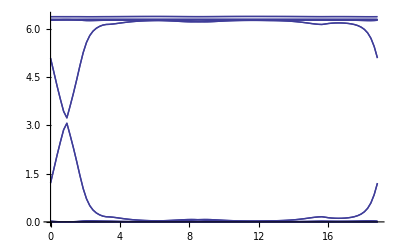

```mathematica
DiscretePlot[Piecewise[{{FCOR[T,0],T≥0&&T<Pi},{FCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{FCOR[3Pi-T,Pi],T≥2Pi&&T<4Pi},{FCOR[-Pi,5Pi-T],T≥4Pi&&T≤5Pi},{FCOR[-6Pi+T,0],T≥5Pi&&T≤6Pi}}],{T,0,6Pi,6Pi/100},Filling->None,Evaluate[Joined->True]]
```

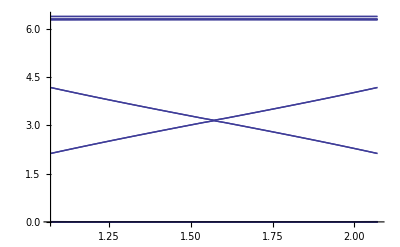

```mathematica
DiscretePlot[FCOR[T,0],{T,Pi/2-0.5,Pi/2+0.5,1/30},Filling->None,Evaluate[Joined->True]]
```

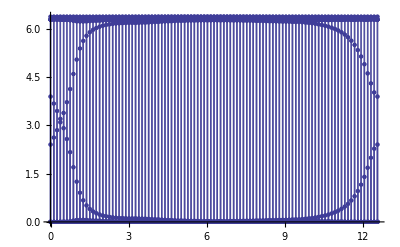

```mathematica
DiscretePlot[Piecewise[{{FCOR[T,0],T≥0&&T<Pi},{FCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{FCOR[3Pi-T,Pi],T≥2Pi&&T<3Pi},{FCOR[0,4Pi-T],T≥3Pi&&T≤4Pi}}],{T,0,4Pi,4Pi/100},FillingStyle->None]
```

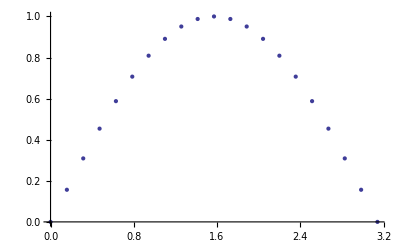

```mathematica
DiscretePlot[Sin[x],{x,0,Pi,Pi/20},Filling->None]
```

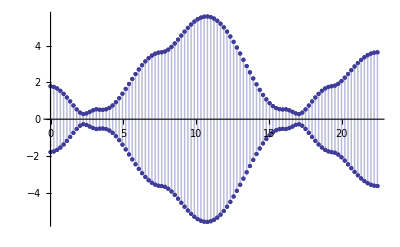

```mathematica
DiscretePlot[Piecewise[{{F[Pi-tt,0,0],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi,(4+Sqrt[2]+Sqrt[3])Pi/100},FillingStyle->None]
```

### Double hamiltonian with different parameters edge states entanglement entropy

```mathematica
AB={1,2}
```

{1,2}

```mathematica
AB[[2]]
```

2

```mathematica
ab[1]=1
ab[2]=2
ab[3]=3
```

1

2

3

```mathematica
ab
```

ab

```mathematica
Find the eigensystem and choose the two lower bands as VEC
```

```mathematica
DESYS[kx_,ky_,kz_]:=Eigensystem[DHam[kx,ky,kz,Pi+0.1,-Pi+0.15]]
DVEC[kx_,ky_,kz_]:=(Clear[VEC];For[i=1;j=1,i≤8,i++,If[DESYS[kx,ky,kz][[1]][[i]]<0,VEC[j]=DESYS[kx,ky,kz][[2]][[i]];j++]];{VEC[1],VEC[2],VEC[3],VEC[4]});
```

```mathematica
DVEC[1,1,1]
```

{{0.202723-0.0649974 ⅈ,-0.439198-0.0383853 ⅈ,-0.0185707-0.0706208 ⅈ,-0.392522+0.16443 ⅈ,0.16333-0.113092 ⅈ,-0.711985-0.0438763 ⅈ,0.140293-0.0643105 ⅈ,-0.0416651},{-0.0228793+0.0693449 ⅈ,0.381665+0.188262 ⅈ,-0.198341-0.0773435 ⅈ,-0.440727+0.0112981 ⅈ,-0.136072-0.072818 ⅈ,-0.0415862-0.00256276 ⅈ,0.156065+0.122924 ⅈ,0.713335},{-0.0355831-0.0122288 ⅈ,-0.164644-0.251576 ⅈ,0.175401+0.118588 ⅈ,0.638221-0.172914 ⅈ,-0.045512-0.104171 ⅈ,-0.315077+0.0755946 ⅈ,0.117949+0.0693386 ⅈ,0.538054},{0.142893-0.156237 ⅈ,-0.66095-0.019243 ⅈ,0.0317481-0.020193 ⅈ,-0.101407+0.283046 ⅈ,-0.0985169+0.094943 ⅈ,0.523206-0.12553 ⅈ,-0.0199525+0.111915 ⅈ,0.324018}}

```mathematica
DVEC[1,1,1][[1]]
```

{0.202723-0.0649974 ⅈ,-0.439198-0.0383853 ⅈ,-0.0185707-0.0706208 ⅈ,-0.392522+0.16443 ⅈ,0.16333-0.113092 ⅈ,-0.711985-0.0438763 ⅈ,0.140293-0.0643105 ⅈ,-0.0416651}

```mathematica
Build correlation function C

define numerical integral function
```

```mathematica
DINT[y_,kx_,kz_,LL_,HL_,i_,j_]:=(Clear[int];
For[ii=LL;int=0,ii≤HL,ii=ii+0.1,int+=0.1y[kx,ii,kz,i,j]];int)
```

```mathematica
define the Core of Correlation function for integral
```

```mathematica
DCORE[kx_,ky_,kz_,i_,j_]:=Exp[I (i-j) ky](KroneckerProduct[Conjugate[DVEC[kx,ky,kz][[1]]],DVEC[kx,ky,kz][[1]]]+KroneckerProduct[Conjugate[DVEC[kx,ky,kz][[2]]],DVEC[kx,ky,kz][[2]]]+KroneckerProduct[Conjugate[DVEC[kx,ky,kz][[3]]],DVEC[kx,ky,kz][[3]]]+KroneckerProduct[Conjugate[DVEC[kx,ky,kz][[4]]],DVEC[kx,ky,kz][[4]]])
```

```mathematica
define the Correlation function matrix,with 24 by 24
```

```mathematica
DHCOR[kx_,kz_]:=(Clear[DCOR];Clear[DOUT];DOUT=Table[DCOR[i][j],{i,6},{j,6}];For[iii=1,iii≤6,iii++,For[jjj=1,jjj≤6,jjj++,DCOR[iii][jjj]=DINT[DCORE ,kx,kz,-Pi,Pi,iii,jjj]]];DOUT=ArrayFlatten[DOUT])
```

```mathematica
MatrixForm[N[DHCOR[1,1]]]
```

(«1»)

#### eigenvalues of Correlation matrix is Pi, we need plot 1/2-Pi

```mathematica
DFCOR[kx_,kz_]:=Sort[Eigenvalues[DHCOR[kx,kz]]]
```

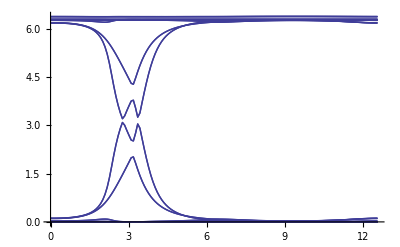

```mathematica
DiscretePlot[Piecewise[{{DFCOR[T,0],T≥0&&T<Pi},{DFCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{DFCOR[3Pi-T,Pi],T≥2Pi&&T<3Pi},{DFCOR[0,4Pi-T],T≥3Pi&&T≤4Pi}}],{T,0,4Pi,4Pi/150},Filling->None,Evaluate[Joined->True]]
```

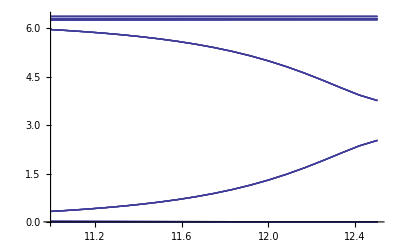

```mathematica
DiscretePlot[Piecewise[{{DFCOR[T,0],T≥0&&T<Pi},{DFCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{DFCOR[3Pi-T,Pi],T≥2Pi&&T<3Pi},{DFCOR[0,4Pi-T],T≥3Pi&&T≤4Pi}}],{T,7Pi/2,4Pi,4Pi/150},Filling->None,Evaluate[Joined->True]]
```

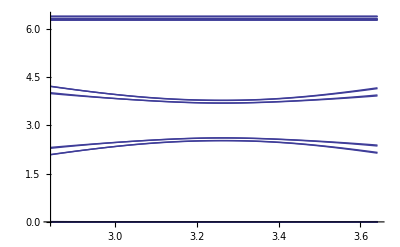

```mathematica
DiscretePlot[DFCOR[T,0],{T,Pi-0.3,Pi+0.5,0.8/50},Filling->None,Evaluate[Joined->True]]
```

### Edge spectrum for physical Hamiltonian with double copies

```mathematica
DSSCON=Table[0,{i,72},{j,72}];
Clear[DSSCOR,DSSCC,DSSC];
DSSCOR[kx_,kz_]:=(DSSCC=DSSCON;Clear[DSSC];DSSC=DSSCON;For[i=1,i≤9,i++,For[j=1,j≤9,j++,For[l=1,l≤8,l++,For[m=1,m≤8,m++,DSSC[[8(i-1)+l]][[8(j-1)+m]]=Integrate[Exp[-I(i-j)ky]DHam[kx,ky,kz,-Pi+0.4,Pi+0.3][[l]][[m]],{ky,-Pi,Pi}]]]]];For[i=1,i≤72,i++,For[j=1,j≤72,j++,DSSCC[[i]][[j]]=DSSC[[i]][[j]]]];DSSCC)
```

```mathematica
DSSR[kx_,kz_]:=Sort[Re[Eigenvalues[N[DSSCOR[kx,kz]]]]]
```

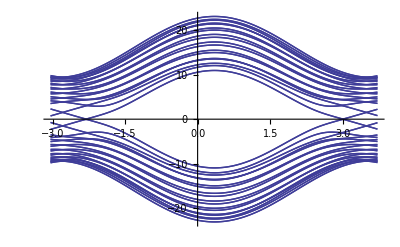

```mathematica
DiscretePlot[DSSR[kx,0],{kx,-Pi+0.1,Pi+0.6,0.4Pi/50},Filling->None,Evaluate[Joined->True]]
```